```mathematica
ClearAll["Global`*"];
```

## The Firm’s Problem

```mathematica
(*Set parameter values*)
alpha=0.5;(*productivity parameter*)
r=1;(*rate of interest*)
p=20;(*Price of goods*)
w=1;(*wage*)
y=100;
(*Define the utility function*)f[l_,k_]:=k^alpha*l^(1-alpha)
```

```mathematica
(*Define the Lagrangian*)
cost[y_,k_,l_,lambda_]:=w*l+r*k-lambda(y-k^alpha*l^(1-alpha))
```

```mathematica
(*Set up the first-order conditions*)
(*eq1=D[cost[y,k,l,lambda],y]==0;*)
eq2=D[cost[y,k,l,lambda],k]==0;
eq3=D[cost[y,k,l,lambda],l]==0;
eq4=D[cost[y,k,l,lambda],lambda]==0;
```

```mathematica
(*Solve the system of equations*)
solution=Solve[{eq2,eq3,eq4},{k,l,lambda}]
```

{{k→100.,l→100.,lambda→-2.}}

```mathematica
costStar=cost[l/.solution, k/.solution][[1]];
lStar=l/.solution[[1]];
kStar=k/.solution[[1]];
List[costStar,lStar,kStar]
```

{{100.},100.,100.}

```mathematica
Plot3D[
cost[y,l,k],{l,0,500},{k,0,500}
]
```

-Graphics3D-

```mathematica
costPlot = Plot3D[
cost[l,k],{l,0,500},{k,0,500}
];
optimalInputs3D=Flatten[{lStar,kStar,costStar}];
optimalPoint3D[a_]:=
Graphics3D[
{Red,Ball[a,50]}
];
```

```mathematica
Show[
costPlot,
 optimalPoint3D[optimalInputs3D]
]
```

-Graphics3D-

```mathematica
indiCurves = 
ContourPlot[
U[c1,c2],{c1,0,2m/p},{c2,0,2m(1+r)/p},
Contours->5,
ContourShading->None,
PlotLegends->Automatic,
FrameLabel->{"Consumption in Period 1","Consumption in Period 2"},
PlotLabel->"Indifference Curves and the Worker's Budget Line"
];
```

```mathematica
maxIndiCurve=
ContourPlot[
U[c1,c2]==utilityStar,
{c1,0,2m/p},{c2,0,3*m/p},
ContourStyle->Blue
];
```

```mathematica
budget=
Plot[
m(2+r)/p-c1(1+r),{c1,0,m},
PlotStyle->Directive[Blue,Thick]
];
```

```mathematica
optimalBundle ={c1Star,c2Star}
```

{41.6667,62.5}

```mathematica
optimalPoint[a_]:=
Graphics[
{Red,PointSize[Large],Point[a]}
];
```

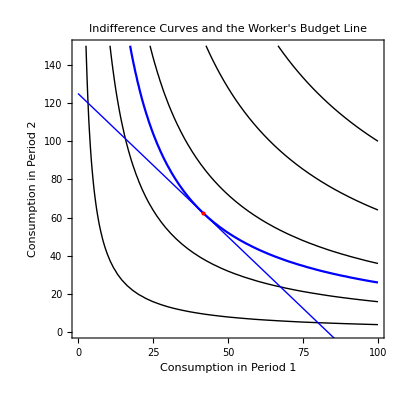

```mathematica
Show[
indiCurves,maxIndiCurve,budget, optimalPoint[optimalBundle]
]
```

```mathematica
Manipulate[Show[]] (*Changing alpha, wage and prices. Use CobbDouglas shortcut*)
```

Manipulate[]